## CommonTimeDomain-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xlr8r.m
<<Cellzilla2D.m
```

xCellerator 0.95 (28-Feb-2014) loaded Tue 6 Jun 2017 17:14:50
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 17:14:50
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Generate 50 random vertices to use a Voronoi Centers

```mathematica
r:=RandomReal[{0,100}]; 
vertices=Table[{r,r}, {10}];
```

Use the Voronoi Centers to generate a tissue with 5 cells using the Bounded-Cell-Voronoi algorithm

```mathematica
w=BoundedCellVoronoi[vertices];
```

Show the tissue and the Voronoi centers (Red)

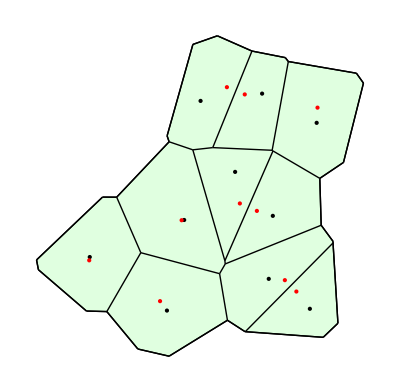

```mathematica
ShowTissue[w, Epilog->{ Point[Centeroid[w]], Red, Point[vertices]}]
```

Define the Cellerator Network in a Single Cell

```mathematica
MyReactions = {{Underoverscript[X⟺XP, ZP, Z],MM[K,v,K,v]}, {Underoverscript[Y⟺YP, XP, X],MM[K,v,K,v]},
   {Underoverscript[Z⟺ZP, YP, Y],MM[K,v,K,v]}};
```

Generate the Reactions in the big network

```mathematica
bignet=CelleratorNetwork[w,
"Reactions"-> MyReactions,
"Diffusion"-> {{X,DX},{Y,DY},{Z,DZ}}];
```

10 Cells.

6 internal reactions in each cell.

60 intracellular reactions.

102 diffusion reactions.

162 total reactions.

Define some random initial conditions

```mathematica
r:=RandomReal[{0,2}]; 
MyIC=Sort[Flatten[{X[#]-> r, Y[#]-> r, Z[#]-> r, XP[#]-> r, YP[#]-> r, ZP[#]-> r}&/@Range[10]]];
```

Define the Paraemters and run a single simulation

```mathematica
MyParameters = {v -> 1, K -> .5, DX-> 13, DY-> 15, DZ-> 11};
```

```mathematica
mysim = run[bignet, {0, 25}, "Parameters"->MyParameters, "IC"-> MyIC]
```

{{X[1]→InterpolatingFunction[{{0., 25.}}, <>],X[2]→InterpolatingFunction[{{0., 25.}}, <>],X[3]→InterpolatingFunction[{{0., 25.}}, <>],X[4]→InterpolatingFunction[{{0., 25.}}, <>],X[5]→InterpolatingFunction[{{0., 25.}}, <>],X[6]→InterpolatingFunction[{{0., 25.}}, <>],X[7]→InterpolatingFunction[{{0., 25.}}, <>],X[8]→InterpolatingFunction[{{0., 25.}}, <>],X[9]→InterpolatingFunction[{{0., 25.}}, <>],X[10]→InterpolatingFunction[{{0., 25.}}, <>],XP[1]→InterpolatingFunction[{{0., 25.}}, <>],XP[2]→InterpolatingFunction[{{0., 25.}}, <>],XP[3]→InterpolatingFunction[{{0., 25.}}, <>],XP[4]→InterpolatingFunction[{{0., 25.}}, <>],XP[5]→InterpolatingFunction[{{0., 25.}}, <>],XP[6]→InterpolatingFunction[{{0., 25.}}, <>],XP[7]→InterpolatingFunction[{{0., 25.}}, <>],XP[8]→InterpolatingFunction[{{0., 25.}}, <>],XP[9]→InterpolatingFunction[{{0., 25.}}, <>],XP[10]→InterpolatingFunction[{{0., 25.}}, <>],Y[1]→InterpolatingFunction[{{0., 25.}}, <>],Y[2]→InterpolatingFunction[{{0., 25.}}, <>],Y[3]→InterpolatingFunction[{{0., 25.}}, <>],Y[4]→InterpolatingFunction[{{0., 25.}}, <>],Y[5]→InterpolatingFunction[{{0., 25.}}, <>],Y[6]→InterpolatingFunction[{{0., 25.}}, <>],Y[7]→InterpolatingFunction[{{0., 25.}}, <>],Y[8]→InterpolatingFunction[{{0., 25.}}, <>],Y[9]→InterpolatingFunction[{{0., 25.}}, <>],Y[10]→InterpolatingFunction[{{0., 25.}}, <>],YP[1]→InterpolatingFunction[{{0., 25.}}, <>],YP[2]→InterpolatingFunction[{{0., 25.}}, <>],YP[3]→InterpolatingFunction[{{0., 25.}}, <>],YP[4]→InterpolatingFunction[{{0., 25.}}, <>],YP[5]→InterpolatingFunction[{{0., 25.}}, <>],YP[6]→InterpolatingFunction[{{0., 25.}}, <>],YP[7]→InterpolatingFunction[{{0., 25.}}, <>],YP[8]→InterpolatingFunction[{{0., 25.}}, <>],YP[9]→InterpolatingFunction[{{0., 25.}}, <>],YP[10]→InterpolatingFunction[{{0., 25.}}, <>],Z[1]→InterpolatingFunction[{{0., 25.}}, <>],Z[2]→InterpolatingFunction[{{0., 25.}}, <>],Z[3]→InterpolatingFunction[{{0., 25.}}, <>],Z[4]→InterpolatingFunction[{{0., 25.}}, <>],Z[5]→InterpolatingFunction[{{0., 25.}}, <>],Z[6]→InterpolatingFunction[{{0., 25.}}, <>],Z[7]→InterpolatingFunction[{{0., 25.}}, <>],Z[8]→InterpolatingFunction[{{0., 25.}}, <>],Z[9]→InterpolatingFunction[{{0., 25.}}, <>],Z[10]→InterpolatingFunction[{{0., 25.}}, <>],ZP[1]→InterpolatingFunction[{{0., 25.}}, <>],ZP[2]→InterpolatingFunction[{{0., 25.}}, <>],ZP[3]→InterpolatingFunction[{{0., 25.}}, <>],ZP[4]→InterpolatingFunction[{{0., 25.}}, <>],ZP[5]→InterpolatingFunction[{{0., 25.}}, <>],ZP[6]→InterpolatingFunction[{{0., 25.}}, <>],ZP[7]→InterpolatingFunction[{{0., 25.}}, <>],ZP[8]→InterpolatingFunction[{{0., 25.}}, <>],ZP[9]→InterpolatingFunction[{{0., 25.}}, <>],ZP[10]→InterpolatingFunction[{{0., 25.}}, <>]}}

```mathematica
CommonTimeDomain[mysim]
```

{0.,25.}